```mathematica
mathnum=1;
```

```mathematica
formnum=13;
```

```mathematica
<<NLOcompare.m
```

FeynCalc 9.0.1. For help, use the documentation center, check out the wiki or write to the mailing list.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

Package-X v1.0.4, by Hiren H. Patel

Contract::shdw: Symbol TraditionalForm`"Contract" appears in multiple contexts TraditionalForm`{"X`IndexAlg`", "FeynCalc`"}; definitions in context TraditionalForm`"X`IndexAlg`" may shadow or be shadowed by other definitions.

DiracMatrix::shdw: Symbol TraditionalForm`"DiracMatrix" appears in multiple contexts TraditionalForm`{"X`Spur`", "FeynCalc`"}; definitions in context TraditionalForm`"X`Spur`" may shadow or be shadowed by other definitions.

For more information, see the

```mathematica
<<renormAmpWest.res
```

```mathematica
Diagr=<<test/diagrBcnlo.m;
(* Amp =<<AmpBcnlo`; *)
AmpbeforeApart=<<test/AmpbeforeApartBcBc.m;
AmpafterFire=<<test/AmpafterFireBcBc.m;
```

```mathematica
Print[DateString[]];
```

Thu 11 Aug 2016 00:44:12

```mathematica
DiaMathRes[mathnum]
```

stage 1: Thu 11 Aug 2016 00:44:14

stage 2: Thu 11 Aug 2016 00:44:14

stage 3: Thu 11 Aug 2016 00:44:16

-(4 e IntF(1/(OverBar[k1]^2-2 r (OverBar[k1]·OverBar[p3])),k1) P1(mu) g_s^4)/(3 m^2 (-1+r)^4 r s (s/m^2-4))+(16 e IntF(1/1,k1) P1(mu) g_s^4)/(27 m^2 (1)^4 r^2 s (s/m^2-4))+129+ϵ (103+(16 e IntF(1/1,k1) P2(mu) g_s^4)/(27 (1)^4 s (s/m^2-4)))
 |  |  |  |

```mathematica
Print[DateString[]];
```

Thu 11 Aug 2016 00:44:18

```mathematica
tmp=DiaCompareCheck[mathnum,formnum,1.5,4.9,175,15^2]
```

stage 1: Thu 11 Aug 2016 00:44:20

stage 2: Thu 11 Aug 2016 00:44:20

stage 3: Thu 11 Aug 2016 00:44:22

stage 4: Thu 11 Aug 2016 00:44:22

stage 5: Thu 11 Aug 2016 00:44:29

stage 6: Thu 11 Aug 2016 00:44:29

stage 7: Thu 11 Aug 2016 00:44:38

mathres =

-0.0000147204 AA(5) eps C[174.516,2.25,131.891,1.5,1.5,0]+2.86191×10^-6 AA(7) eps C[174.516,2.25,131.891,1.5,1.5,0]+0.0000222207 AA(5) C[174.516,2.25,131.891,1.5,1.5,0]-0.0000113953 AA(7) C[174.516,2.25,131.891,1.5,1.5,0]+2.83944×10^-7 AA(5) eps B(131.891,1.5,1.5)-2.8182×10^-7 AA(5) eps B(174.516,0,1.5)-1.80672×10^-7 AA(7) eps B(131.891,1.5,1.5)+2.08229×10^-7 AA(7) eps B(174.516,0,1.5)-7.88538×10^-7 AA(5) B(131.891,1.5,1.5)+8.95262×10^-7 AA(5) B(174.516,0,1.5)+5.01742×10^-7 AA(7) B(131.891,1.5,1.5)-5.78442×10^-7 AA(7) B(174.516,0,1.5)-2.10255×10^-8 A(1.5) AA(5) eps+2.18846×10^-8 A(1.5) AA(7) eps-6.32582×10^-8 A(1.5) AA(5)+3.07482×10^-8 A(1.5) AA(7)

formres =

-6.38118×10^-6 AA(5) eps C[174.516,2.25,131.891,1.5,1.5,0]-(AA(5) eps C[174.516,2.25,131.891,1.5,1.5,0])/(12150 π^2)+2.86191×10^-6 AA(7) eps C[174.516,2.25,131.891,1.5,1.5,0]+(AA(5) C[174.516,2.25,131.891,1.5,1.5,0])/(12150 π^2)+0.0000138815 AA(5) C[174.516,2.25,131.891,1.5,1.5,0]-0.0000113953 AA(7) C[174.516,2.25,131.891,1.5,1.5,0]+2.83944×10^-7 AA(5) eps B(131.891,1.5,1.5)-2.8182×10^-7 AA(5) eps B(174.516,0,1.5)-1.80672×10^-7 AA(7) eps B(131.891,1.5,1.5)+2.08229×10^-7 AA(7) eps B(174.516,0,1.5)-7.88538×10^-7 AA(5) B(131.891,1.5,1.5)+8.95262×10^-7 AA(5) B(174.516,0,1.5)+5.01742×10^-7 AA(7) B(131.891,1.5,1.5)-5.78442×10^-7 AA(7) B(174.516,0,1.5)-2.10255×10^-8 A(1.5) AA(5) eps+2.18846×10^-8 A(1.5) AA(7) eps-6.32582×10^-8 A(1.5) AA(5)+3.07482×10^-8 A(1.5) AA(7)

0

```mathematica
DiaCompare[mathnum,formnum,1.5,4.9,175,15^2]
```

stage 1: Thu 11 Aug 2016 00:44:40

stage 2: Thu 11 Aug 2016 00:44:40

stage 3: Thu 11 Aug 2016 00:44:41

stage 4: Thu 11 Aug 2016 00:44:42

stage 5: Thu 11 Aug 2016 00:44:45

stage 6: Thu 11 Aug 2016 00:44:46

stage 7: Thu 11 Aug 2016 00:44:46

0

```mathematica
dianumlist={{1,13},{2,14},{3,31},{4,32},{5,33},{6,34},{7,15},{8,16},{9,43},{10,44},{11,45},{12,46},{13,22},{14,23},{15,24},{16,25},{29,26},{30,27},{31,30},{32,28},{33,29},{34,35},{35,36},{36,37},{37,38},{38,39},{39,40},{40,41},{41,42},{42,17},{43,18},{44,21},{45,19},{46,20},{47,48},{48,50},{49,47},{50,49},{51,57},{52,58},{53,59},{54,60},{55,61},{56,62},{57,63},{58,64},{59,65},{60,67},{61,68},{62,69},{63,70},{64,71},{65,72},{66,73},{67,74},{68,66},{69,88},{70,89},{71,90},{72,91},{73,92},{74,93},{75,94},{76,95},{77,87},{78,97},{79,98},{80,99},{81,100},{82,101},{83,102},{84,103},{85,104},{86,96}};
```

```mathematica
Print[DateString[]];
```

Thu 11 Aug 2016 00:44:46

```mathematica
diff= DiaCompareList[dianumlist,1.5,4.9,175,15^2]
```

Checking diagrams with numbers 1 and 13

stage 1: Thu 11 Aug 2016 00:44:46

stage 2: Thu 11 Aug 2016 00:44:46

stage 3: Thu 11 Aug 2016 00:44:49

stage 4: Thu 11 Aug 2016 00:44:49

stage 5: Thu 11 Aug 2016 00:44:52

stage 6: Thu 11 Aug 2016 00:44:52

stage 7: Thu 11 Aug 2016 00:44:53

Checking diagrams with numbers 2 and 14

stage 1: Thu 11 Aug 2016 00:44:54

stage 2: Thu 11 Aug 2016 00:44:54

stage 3: Thu 11 Aug 2016 00:44:55

stage 4: Thu 11 Aug 2016 00:44:55

stage 5: Thu 11 Aug 2016 00:45:00

stage 6: Thu 11 Aug 2016 00:45:00

stage 7: Thu 11 Aug 2016 00:45:01

Checking diagrams with numbers 3 and 31

stage 1: Thu 11 Aug 2016 00:45:01

stage 2: Thu 11 Aug 2016 00:45:01

stage 3: Thu 11 Aug 2016 00:45:02

stage 4: Thu 11 Aug 2016 00:45:02

stage 5: Thu 11 Aug 2016 00:45:04

stage 6: Thu 11 Aug 2016 00:45:04

stage 7: Thu 11 Aug 2016 00:45:09

Checking diagrams with numbers 4 and 32

stage 1: Thu 11 Aug 2016 00:45:10

stage 2: Thu 11 Aug 2016 00:45:10

stage 3: Thu 11 Aug 2016 00:45:11

stage 4: Thu 11 Aug 2016 00:45:11

stage 5: Thu 11 Aug 2016 00:45:13

stage 6: Thu 11 Aug 2016 00:45:13

stage 7: Thu 11 Aug 2016 00:45:13

Checking diagrams with numbers 5 and 33

stage 1: Thu 11 Aug 2016 00:45:15

stage 2: Thu 11 Aug 2016 00:45:15

stage 3: Thu 11 Aug 2016 00:45:17

stage 4: Thu 11 Aug 2016 00:45:17

stage 5: Thu 11 Aug 2016 00:45:25

stage 6: Thu 11 Aug 2016 00:45:26

stage 7: Thu 11 Aug 2016 00:45:26

Checking diagrams with numbers 6 and 34

stage 1: Thu 11 Aug 2016 00:45:28

stage 2: Thu 11 Aug 2016 00:45:28

stage 3: Thu 11 Aug 2016 00:45:30

stage 4: Thu 11 Aug 2016 00:45:30

stage 5: Thu 11 Aug 2016 00:45:38

stage 6: Thu 11 Aug 2016 00:45:39

stage 7: Thu 11 Aug 2016 00:45:54

Checking diagrams with numbers 7 and 15

stage 1: Thu 11 Aug 2016 00:45:56

stage 2: Thu 11 Aug 2016 00:45:56

stage 3: Thu 11 Aug 2016 00:45:58

stage 4: Thu 11 Aug 2016 00:45:58

stage 5: Thu 11 Aug 2016 00:46:03

stage 6: Thu 11 Aug 2016 00:46:04

stage 7: Thu 11 Aug 2016 00:46:04

Checking diagrams with numbers 8 and 16

stage 1: Thu 11 Aug 2016 00:46:05

stage 2: Thu 11 Aug 2016 00:46:05

stage 3: Thu 11 Aug 2016 00:46:07

stage 4: Thu 11 Aug 2016 00:46:07

stage 5: Thu 11 Aug 2016 00:46:11

stage 6: Thu 11 Aug 2016 00:46:12

stage 7: Thu 11 Aug 2016 00:46:12

Checking diagrams with numbers 9 and 43

stage 1: Thu 11 Aug 2016 00:46:12

stage 2: Thu 11 Aug 2016 00:46:12

stage 3: Thu 11 Aug 2016 00:46:13

stage 4: Thu 11 Aug 2016 00:46:13

stage 5: Thu 11 Aug 2016 00:46:15

stage 6: Thu 11 Aug 2016 00:46:15

stage 7: Thu 11 Aug 2016 00:46:20

Checking diagrams with numbers 10 and 44

stage 1: Thu 11 Aug 2016 00:46:21

stage 2: Thu 11 Aug 2016 00:46:21

stage 3: Thu 11 Aug 2016 00:46:22

stage 4: Thu 11 Aug 2016 00:46:22

stage 5: Thu 11 Aug 2016 00:46:24

stage 6: Thu 11 Aug 2016 00:46:24

stage 7: Thu 11 Aug 2016 00:46:25

Checking diagrams with numbers 11 and 45

stage 1: Thu 11 Aug 2016 00:46:27

stage 2: Thu 11 Aug 2016 00:46:27

stage 3: Thu 11 Aug 2016 00:46:29

stage 4: Thu 11 Aug 2016 00:46:29

stage 5: Thu 11 Aug 2016 00:46:37

stage 6: Thu 11 Aug 2016 00:46:38

stage 7: Thu 11 Aug 2016 00:46:43

Checking diagrams with numbers 12 and 46

stage 1: Thu 11 Aug 2016 00:46:45

stage 2: Thu 11 Aug 2016 00:46:45

stage 3: Thu 11 Aug 2016 00:46:48

stage 4: Thu 11 Aug 2016 00:46:48

stage 5: Thu 11 Aug 2016 00:46:56

stage 6: Thu 11 Aug 2016 00:46:56

stage 7: Thu 11 Aug 2016 00:46:56

Checking diagrams with numbers 13 and 22

stage 1: Thu 11 Aug 2016 00:46:58

stage 2: Thu 11 Aug 2016 00:46:58

stage 3: Thu 11 Aug 2016 00:46:59

stage 4: Thu 11 Aug 2016 00:46:59

stage 5: Thu 11 Aug 2016 00:47:04

stage 6: Thu 11 Aug 2016 00:47:05

stage 7: Thu 11 Aug 2016 00:47:13

Checking diagrams with numbers 14 and 23

stage 1: Thu 11 Aug 2016 00:47:14

stage 2: Thu 11 Aug 2016 00:47:14

stage 3: Thu 11 Aug 2016 00:47:15

stage 4: Thu 11 Aug 2016 00:47:15

stage 5: Thu 11 Aug 2016 00:47:20

stage 6: Thu 11 Aug 2016 00:47:20

stage 7: Thu 11 Aug 2016 00:47:21

Checking diagrams with numbers 15 and 24

stage 1: Thu 11 Aug 2016 00:47:23

stage 2: Thu 11 Aug 2016 00:47:23

stage 3: Thu 11 Aug 2016 00:47:24

stage 4: Thu 11 Aug 2016 00:47:25

stage 5: Thu 11 Aug 2016 00:47:30

stage 6: Thu 11 Aug 2016 00:47:31

stage 7: Thu 11 Aug 2016 00:47:31

Checking diagrams with numbers 16 and 25

stage 1: Thu 11 Aug 2016 00:47:32

stage 2: Thu 11 Aug 2016 00:47:32

stage 3: Thu 11 Aug 2016 00:47:33

stage 4: Thu 11 Aug 2016 00:47:34

stage 5: Thu 11 Aug 2016 00:47:38

stage 6: Thu 11 Aug 2016 00:47:38

stage 7: Thu 11 Aug 2016 00:47:38

Checking diagrams with numbers 29 and 26

stage 1: Thu 11 Aug 2016 00:47:40

stage 2: Thu 11 Aug 2016 00:47:40

stage 3: Thu 11 Aug 2016 00:47:42

stage 4: Thu 11 Aug 2016 00:47:42

stage 5: Thu 11 Aug 2016 00:47:49

stage 6: Thu 11 Aug 2016 00:47:50

stage 7: Thu 11 Aug 2016 00:47:57

Checking diagrams with numbers 30 and 27

stage 1: Thu 11 Aug 2016 00:47:59

stage 2: Thu 11 Aug 2016 00:47:59

stage 3: Thu 11 Aug 2016 00:48:00

stage 4: Thu 11 Aug 2016 00:48:00

stage 5: Thu 11 Aug 2016 00:48:06

stage 6: Thu 11 Aug 2016 00:48:06

stage 7: Thu 11 Aug 2016 00:48:07

Checking diagrams with numbers 31 and 30

stage 1: Thu 11 Aug 2016 00:48:12

stage 2: Thu 11 Aug 2016 00:48:12

stage 3: Thu 11 Aug 2016 00:48:17

stage 4: Thu 11 Aug 2016 00:48:17

stage 5: Thu 11 Aug 2016 00:48:34

stage 6: Thu 11 Aug 2016 00:48:35

stage 7: Thu 11 Aug 2016 00:48:35

Checking diagrams with numbers 32 and 28

stage 1: Thu 11 Aug 2016 00:48:38

stage 2: Thu 11 Aug 2016 00:48:38

stage 3: Thu 11 Aug 2016 00:48:41

stage 4: Thu 11 Aug 2016 00:48:41

stage 5: Thu 11 Aug 2016 00:48:53

stage 6: Thu 11 Aug 2016 00:48:53

stage 7: Thu 11 Aug 2016 00:48:59

Checking diagrams with numbers 33 and 29

stage 1: Thu 11 Aug 2016 00:49:02

stage 2: Thu 11 Aug 2016 00:49:02

stage 3: Thu 11 Aug 2016 00:49:05

stage 4: Thu 11 Aug 2016 00:49:05

stage 5: Thu 11 Aug 2016 00:49:16

stage 6: Thu 11 Aug 2016 00:49:16

stage 7: Thu 11 Aug 2016 00:49:17

Checking diagrams with numbers 34 and 35

stage 1: Thu 11 Aug 2016 00:49:17

stage 2: Thu 11 Aug 2016 00:49:17

stage 3: Thu 11 Aug 2016 00:49:18

stage 4: Thu 11 Aug 2016 00:49:18

stage 5: Thu 11 Aug 2016 00:49:19

stage 6: Thu 11 Aug 2016 00:49:19

stage 7: Thu 11 Aug 2016 00:49:25

Checking diagrams with numbers 35 and 36

stage 1: Thu 11 Aug 2016 00:49:26

stage 2: Thu 11 Aug 2016 00:49:26

stage 3: Thu 11 Aug 2016 00:49:26

stage 4: Thu 11 Aug 2016 00:49:26

stage 5: Thu 11 Aug 2016 00:49:28

stage 6: Thu 11 Aug 2016 00:49:28

stage 7: Thu 11 Aug 2016 00:49:28

Checking diagrams with numbers 36 and 37

stage 1: Thu 11 Aug 2016 00:49:30

stage 2: Thu 11 Aug 2016 00:49:30

stage 3: Thu 11 Aug 2016 00:49:32

stage 4: Thu 11 Aug 2016 00:49:32

stage 5: Thu 11 Aug 2016 00:49:39

stage 6: Thu 11 Aug 2016 00:49:39

stage 7: Thu 11 Aug 2016 00:49:39

Checking diagrams with numbers 37 and 38

stage 1: Thu 11 Aug 2016 00:49:41

stage 2: Thu 11 Aug 2016 00:49:41

stage 3: Thu 11 Aug 2016 00:49:43

stage 4: Thu 11 Aug 2016 00:49:43

stage 5: Thu 11 Aug 2016 00:49:51

stage 6: Thu 11 Aug 2016 00:49:52

stage 7: Thu 11 Aug 2016 00:49:53

Checking diagrams with numbers 38 and 39

stage 1: Thu 11 Aug 2016 00:49:53

stage 2: Thu 11 Aug 2016 00:49:53

stage 3: Thu 11 Aug 2016 00:49:54

stage 4: Thu 11 Aug 2016 00:49:54

stage 5: Thu 11 Aug 2016 00:49:55

stage 6: Thu 11 Aug 2016 00:49:55

stage 7: Thu 11 Aug 2016 00:50:00

Checking diagrams with numbers 39 and 40

stage 1: Thu 11 Aug 2016 00:50:01

stage 2: Thu 11 Aug 2016 00:50:01

stage 3: Thu 11 Aug 2016 00:50:01

stage 4: Thu 11 Aug 2016 00:50:01

stage 5: Thu 11 Aug 2016 00:50:02

stage 6: Thu 11 Aug 2016 00:50:02

stage 7: Thu 11 Aug 2016 00:50:02

Checking diagrams with numbers 40 and 41

stage 1: Thu 11 Aug 2016 00:50:04

stage 2: Thu 11 Aug 2016 00:50:04

stage 3: Thu 11 Aug 2016 00:50:06

stage 4: Thu 11 Aug 2016 00:50:06

stage 5: Thu 11 Aug 2016 00:50:13

stage 6: Thu 11 Aug 2016 00:50:14

stage 7: Thu 11 Aug 2016 00:50:14

Checking diagrams with numbers 41 and 42

stage 1: Thu 11 Aug 2016 00:50:16

stage 2: Thu 11 Aug 2016 00:50:16

stage 3: Thu 11 Aug 2016 00:50:18

stage 4: Thu 11 Aug 2016 00:50:18

stage 5: Thu 11 Aug 2016 00:50:26

stage 6: Thu 11 Aug 2016 00:50:26

stage 7: Thu 11 Aug 2016 00:50:27

Checking diagrams with numbers 42 and 17

stage 1: Thu 11 Aug 2016 00:50:29

stage 2: Thu 11 Aug 2016 00:50:29

stage 3: Thu 11 Aug 2016 00:50:31

stage 4: Thu 11 Aug 2016 00:50:31

stage 5: Thu 11 Aug 2016 00:50:37

stage 6: Thu 11 Aug 2016 00:50:37

stage 7: Thu 11 Aug 2016 00:50:45

Checking diagrams with numbers 43 and 18

stage 1: Thu 11 Aug 2016 00:50:46

stage 2: Thu 11 Aug 2016 00:50:46

stage 3: Thu 11 Aug 2016 00:50:48

stage 4: Thu 11 Aug 2016 00:50:49

stage 5: Thu 11 Aug 2016 00:50:53

stage 6: Thu 11 Aug 2016 00:50:53

stage 7: Thu 11 Aug 2016 00:50:53

Checking diagrams with numbers 44 and 21

stage 1: Thu 11 Aug 2016 00:50:59

stage 2: Thu 11 Aug 2016 00:50:59

stage 3: Thu 11 Aug 2016 00:51:04

stage 4: Thu 11 Aug 2016 00:51:04

stage 5: Thu 11 Aug 2016 00:51:21

stage 6: Thu 11 Aug 2016 00:51:22

stage 7: Thu 11 Aug 2016 00:51:22

Checking diagrams with numbers 45 and 19

stage 1: Thu 11 Aug 2016 00:51:27

stage 2: Thu 11 Aug 2016 00:51:27

stage 3: Thu 11 Aug 2016 00:51:30

stage 4: Thu 11 Aug 2016 00:51:30

stage 5: Thu 11 Aug 2016 00:51:39

stage 6: Thu 11 Aug 2016 00:51:40

stage 7: Thu 11 Aug 2016 00:51:40

Checking diagrams with numbers 46 and 20

stage 1: Thu 11 Aug 2016 00:51:44

stage 2: Thu 11 Aug 2016 00:51:44

stage 3: Thu 11 Aug 2016 00:51:48

stage 4: Thu 11 Aug 2016 00:51:48

stage 5: Thu 11 Aug 2016 00:51:58

stage 6: Thu 11 Aug 2016 00:51:59

stage 7: Thu 11 Aug 2016 00:51:59

Checking diagrams with numbers 47 and 48

stage 1: Thu 11 Aug 2016 00:52:10

stage 2: Thu 11 Aug 2016 00:52:10

stage 3: Thu 11 Aug 2016 00:52:19

stage 4: Thu 11 Aug 2016 00:52:20

stage 5: Thu 11 Aug 2016 00:52:53

stage 6: Thu 11 Aug 2016 00:52:55

stage 7: Thu 11 Aug 2016 00:52:56

Checking diagrams with numbers 48 and 50

stage 1: Thu 11 Aug 2016 00:53:05

stage 2: Thu 11 Aug 2016 00:53:06

stage 3: Thu 11 Aug 2016 00:53:19

stage 4: Thu 11 Aug 2016 00:53:20

stage 5: Thu 11 Aug 2016 00:54:00

stage 6: Thu 11 Aug 2016 00:54:01

stage 7: Thu 11 Aug 2016 00:54:02

Checking diagrams with numbers 49 and 47

stage 1: Thu 11 Aug 2016 00:54:12

stage 2: Thu 11 Aug 2016 00:54:13

stage 3: Thu 11 Aug 2016 00:54:23

stage 4: Thu 11 Aug 2016 00:54:24

stage 5: Thu 11 Aug 2016 00:54:57

stage 6: Thu 11 Aug 2016 00:54:59

stage 7: Thu 11 Aug 2016 00:55:00

Checking diagrams with numbers 50 and 49

stage 1: Thu 11 Aug 2016 00:55:05

stage 2: Thu 11 Aug 2016 00:55:06

stage 3: Thu 11 Aug 2016 00:55:11

stage 4: Thu 11 Aug 2016 00:55:11

stage 5: Thu 11 Aug 2016 00:55:36

stage 6: Thu 11 Aug 2016 00:55:37

stage 7: Thu 11 Aug 2016 00:55:38

Checking diagrams with numbers 51 and 57

stage 1: Thu 11 Aug 2016 00:55:38

stage 2: Thu 11 Aug 2016 00:55:38

stage 3: Thu 11 Aug 2016 00:55:39

stage 4: Thu 11 Aug 2016 00:55:39

stage 5: Thu 11 Aug 2016 00:55:39

stage 6: Thu 11 Aug 2016 00:55:39

stage 7: Thu 11 Aug 2016 00:55:39

Checking diagrams with numbers 52 and 58

stage 1: Thu 11 Aug 2016 00:55:39

stage 2: Thu 11 Aug 2016 00:55:39

stage 3: Thu 11 Aug 2016 00:55:40

stage 4: Thu 11 Aug 2016 00:55:40

stage 5: Thu 11 Aug 2016 00:55:42

stage 6: Thu 11 Aug 2016 00:55:42

stage 7: Thu 11 Aug 2016 00:55:42

Checking diagrams with numbers 53 and 59

stage 1: Thu 11 Aug 2016 00:55:42

stage 2: Thu 11 Aug 2016 00:55:42

stage 3: Thu 11 Aug 2016 00:55:43

stage 4: Thu 11 Aug 2016 00:55:43

stage 5: Thu 11 Aug 2016 00:55:45

stage 6: Thu 11 Aug 2016 00:55:45

stage 7: Thu 11 Aug 2016 00:55:51

Checking diagrams with numbers 54 and 60

stage 1: Thu 11 Aug 2016 00:55:52

stage 2: Thu 11 Aug 2016 00:55:52

stage 3: Thu 11 Aug 2016 00:55:52

stage 4: Thu 11 Aug 2016 00:55:52

stage 5: Thu 11 Aug 2016 00:55:52

stage 6: Thu 11 Aug 2016 00:55:52

stage 7: Thu 11 Aug 2016 00:55:52

Checking diagrams with numbers 55 and 61

stage 1: Thu 11 Aug 2016 00:55:52

stage 2: Thu 11 Aug 2016 00:55:52

stage 3: Thu 11 Aug 2016 00:55:52

stage 4: Thu 11 Aug 2016 00:55:53

stage 5: Thu 11 Aug 2016 00:55:53

stage 6: Thu 11 Aug 2016 00:55:53

stage 7: Thu 11 Aug 2016 00:55:53

Checking diagrams with numbers 56 and 62

stage 1: Thu 11 Aug 2016 00:55:53

stage 2: Thu 11 Aug 2016 00:55:53

stage 3: Thu 11 Aug 2016 00:55:54

stage 4: Thu 11 Aug 2016 00:55:54

stage 5: Thu 11 Aug 2016 00:55:56

stage 6: Thu 11 Aug 2016 00:55:56

stage 7: Thu 11 Aug 2016 00:55:56

Checking diagrams with numbers 57 and 63

stage 1: Thu 11 Aug 2016 00:55:57

stage 2: Thu 11 Aug 2016 00:55:57

stage 3: Thu 11 Aug 2016 00:55:57

stage 4: Thu 11 Aug 2016 00:55:57

stage 5: Thu 11 Aug 2016 00:55:57

stage 6: Thu 11 Aug 2016 00:55:57

stage 7: Thu 11 Aug 2016 00:55:57

Checking diagrams with numbers 58 and 64

stage 1: Thu 11 Aug 2016 00:55:57

stage 2: Thu 11 Aug 2016 00:55:57

stage 3: Thu 11 Aug 2016 00:55:58

stage 4: Thu 11 Aug 2016 00:55:58

stage 5: Thu 11 Aug 2016 00:55:58

stage 6: Thu 11 Aug 2016 00:55:58

stage 7: Thu 11 Aug 2016 00:55:58

Checking diagrams with numbers 59 and 65

stage 1: Thu 11 Aug 2016 00:55:59

stage 2: Thu 11 Aug 2016 00:55:59

stage 3: Thu 11 Aug 2016 00:55:59

stage 4: Thu 11 Aug 2016 00:56:00

stage 5: Thu 11 Aug 2016 00:56:02

stage 6: Thu 11 Aug 2016 00:56:02

stage 7: Thu 11 Aug 2016 00:56:02

Checking diagrams with numbers 60 and 67

stage 1: Thu 11 Aug 2016 00:56:03

stage 2: Thu 11 Aug 2016 00:56:03

stage 3: Thu 11 Aug 2016 00:56:03

stage 4: Thu 11 Aug 2016 00:56:03

stage 5: Thu 11 Aug 2016 00:56:03

stage 6: Thu 11 Aug 2016 00:56:03

stage 7: Thu 11 Aug 2016 00:56:03

Checking diagrams with numbers 61 and 68

stage 1: Thu 11 Aug 2016 00:56:04

stage 2: Thu 11 Aug 2016 00:56:04

stage 3: Thu 11 Aug 2016 00:56:05

stage 4: Thu 11 Aug 2016 00:56:05

stage 5: Thu 11 Aug 2016 00:56:06

stage 6: Thu 11 Aug 2016 00:56:06

stage 7: Thu 11 Aug 2016 00:56:06

Checking diagrams with numbers 62 and 69

stage 1: Thu 11 Aug 2016 00:56:07

stage 2: Thu 11 Aug 2016 00:56:07

stage 3: Thu 11 Aug 2016 00:56:08

stage 4: Thu 11 Aug 2016 00:56:08

stage 5: Thu 11 Aug 2016 00:56:09

stage 6: Thu 11 Aug 2016 00:56:10

stage 7: Thu 11 Aug 2016 00:56:14

Checking diagrams with numbers 63 and 70

stage 1: Thu 11 Aug 2016 00:56:15

stage 2: Thu 11 Aug 2016 00:56:15

stage 3: Thu 11 Aug 2016 00:56:15

stage 4: Thu 11 Aug 2016 00:56:15

stage 5: Thu 11 Aug 2016 00:56:15

stage 6: Thu 11 Aug 2016 00:56:15

stage 7: Thu 11 Aug 2016 00:56:15

Checking diagrams with numbers 64 and 71

stage 1: Thu 11 Aug 2016 00:56:15

stage 2: Thu 11 Aug 2016 00:56:15

stage 3: Thu 11 Aug 2016 00:56:15

stage 4: Thu 11 Aug 2016 00:56:15

stage 5: Thu 11 Aug 2016 00:56:15

stage 6: Thu 11 Aug 2016 00:56:15

stage 7: Thu 11 Aug 2016 00:56:16

Checking diagrams with numbers 65 and 72

stage 1: Thu 11 Aug 2016 00:56:16

stage 2: Thu 11 Aug 2016 00:56:16

stage 3: Thu 11 Aug 2016 00:56:16

stage 4: Thu 11 Aug 2016 00:56:16

stage 5: Thu 11 Aug 2016 00:56:18

stage 6: Thu 11 Aug 2016 00:56:19

stage 7: Thu 11 Aug 2016 00:56:19

Checking diagrams with numbers 66 and 73

stage 1: Thu 11 Aug 2016 00:56:19

stage 2: Thu 11 Aug 2016 00:56:19

stage 3: Thu 11 Aug 2016 00:56:19

stage 4: Thu 11 Aug 2016 00:56:19

stage 5: Thu 11 Aug 2016 00:56:19

stage 6: Thu 11 Aug 2016 00:56:20

stage 7: Thu 11 Aug 2016 00:56:20

Checking diagrams with numbers 67 and 74

stage 1: Thu 11 Aug 2016 00:56:20

stage 2: Thu 11 Aug 2016 00:56:20

stage 3: Thu 11 Aug 2016 00:56:20

stage 4: Thu 11 Aug 2016 00:56:20

stage 5: Thu 11 Aug 2016 00:56:20

stage 6: Thu 11 Aug 2016 00:56:21

stage 7: Thu 11 Aug 2016 00:56:21

Checking diagrams with numbers 68 and 66

stage 1: Thu 11 Aug 2016 00:56:21

stage 2: Thu 11 Aug 2016 00:56:21

stage 3: Thu 11 Aug 2016 00:56:22

stage 4: Thu 11 Aug 2016 00:56:22

stage 5: Thu 11 Aug 2016 00:56:26

stage 6: Thu 11 Aug 2016 00:56:27

stage 7: Thu 11 Aug 2016 00:56:27

Checking diagrams with numbers 69 and 88

stage 1: Thu 11 Aug 2016 00:56:27

stage 2: Thu 11 Aug 2016 00:56:28

stage 3: Thu 11 Aug 2016 00:56:28

stage 4: Thu 11 Aug 2016 00:56:28

stage 5: Thu 11 Aug 2016 00:56:28

stage 6: Thu 11 Aug 2016 00:56:28

stage 7: Thu 11 Aug 2016 00:56:28

Checking diagrams with numbers 70 and 89

stage 1: Thu 11 Aug 2016 00:56:28

stage 2: Thu 11 Aug 2016 00:56:28

stage 3: Thu 11 Aug 2016 00:56:29

stage 4: Thu 11 Aug 2016 00:56:29

stage 5: Thu 11 Aug 2016 00:56:29

stage 6: Thu 11 Aug 2016 00:56:30

stage 7: Thu 11 Aug 2016 00:56:30

Checking diagrams with numbers 71 and 90

stage 1: Thu 11 Aug 2016 00:56:30

stage 2: Thu 11 Aug 2016 00:56:30

stage 3: Thu 11 Aug 2016 00:56:30

stage 4: Thu 11 Aug 2016 00:56:30

stage 5: Thu 11 Aug 2016 00:56:31

stage 6: Thu 11 Aug 2016 00:56:32

stage 7: Thu 11 Aug 2016 00:56:37

Checking diagrams with numbers 72 and 91

stage 1: Thu 11 Aug 2016 00:56:37

stage 2: Thu 11 Aug 2016 00:56:38

stage 3: Thu 11 Aug 2016 00:56:38

stage 4: Thu 11 Aug 2016 00:56:38

stage 5: Thu 11 Aug 2016 00:56:38

stage 6: Thu 11 Aug 2016 00:56:38

stage 7: Thu 11 Aug 2016 00:56:38

Checking diagrams with numbers 73 and 92

stage 1: Thu 11 Aug 2016 00:56:38

stage 2: Thu 11 Aug 2016 00:56:38

stage 3: Thu 11 Aug 2016 00:56:38

stage 4: Thu 11 Aug 2016 00:56:38

stage 5: Thu 11 Aug 2016 00:56:38

stage 6: Thu 11 Aug 2016 00:56:38

stage 7: Thu 11 Aug 2016 00:56:38

Checking diagrams with numbers 74 and 93

stage 1: Thu 11 Aug 2016 00:56:39

stage 2: Thu 11 Aug 2016 00:56:39

stage 3: Thu 11 Aug 2016 00:56:39

stage 4: Thu 11 Aug 2016 00:56:39

stage 5: Thu 11 Aug 2016 00:56:40

stage 6: Thu 11 Aug 2016 00:56:41

stage 7: Thu 11 Aug 2016 00:56:41

Checking diagrams with numbers 75 and 94

stage 1: Thu 11 Aug 2016 00:56:41

stage 2: Thu 11 Aug 2016 00:56:41

stage 3: Thu 11 Aug 2016 00:56:41

stage 4: Thu 11 Aug 2016 00:56:41

stage 5: Thu 11 Aug 2016 00:56:41

stage 6: Thu 11 Aug 2016 00:56:42

stage 7: Thu 11 Aug 2016 00:56:42

Checking diagrams with numbers 76 and 95

stage 1: Thu 11 Aug 2016 00:56:42

stage 2: Thu 11 Aug 2016 00:56:42

stage 3: Thu 11 Aug 2016 00:56:42

stage 4: Thu 11 Aug 2016 00:56:42

stage 5: Thu 11 Aug 2016 00:56:42

stage 6: Thu 11 Aug 2016 00:56:42

stage 7: Thu 11 Aug 2016 00:56:42

Checking diagrams with numbers 77 and 87

stage 1: Thu 11 Aug 2016 00:56:43

stage 2: Thu 11 Aug 2016 00:56:43

stage 3: Thu 11 Aug 2016 00:56:43

stage 4: Thu 11 Aug 2016 00:56:43

stage 5: Thu 11 Aug 2016 00:56:46

stage 6: Thu 11 Aug 2016 00:56:46

stage 7: Thu 11 Aug 2016 00:56:46

Checking diagrams with numbers 78 and 97

stage 1: Thu 11 Aug 2016 00:56:47

stage 2: Thu 11 Aug 2016 00:56:47

stage 3: Thu 11 Aug 2016 00:56:47

stage 4: Thu 11 Aug 2016 00:56:47

stage 5: Thu 11 Aug 2016 00:56:47

stage 6: Thu 11 Aug 2016 00:56:47

stage 7: Thu 11 Aug 2016 00:56:47

Checking diagrams with numbers 79 and 98

stage 1: Thu 11 Aug 2016 00:56:48

stage 2: Thu 11 Aug 2016 00:56:48

stage 3: Thu 11 Aug 2016 00:56:48

stage 4: Thu 11 Aug 2016 00:56:48

stage 5: Thu 11 Aug 2016 00:56:49

stage 6: Thu 11 Aug 2016 00:56:49

stage 7: Thu 11 Aug 2016 00:56:50

Checking diagrams with numbers 80 and 99

stage 1: Thu 11 Aug 2016 00:56:50

stage 2: Thu 11 Aug 2016 00:56:50

stage 3: Thu 11 Aug 2016 00:56:51

stage 4: Thu 11 Aug 2016 00:56:51

stage 5: Thu 11 Aug 2016 00:56:51

stage 6: Thu 11 Aug 2016 00:56:52

stage 7: Thu 11 Aug 2016 00:56:52

Checking diagrams with numbers 81 and 100

stage 1: Thu 11 Aug 2016 00:56:52

stage 2: Thu 11 Aug 2016 00:56:52

stage 3: Thu 11 Aug 2016 00:56:52

stage 4: Thu 11 Aug 2016 00:56:52

stage 5: Thu 11 Aug 2016 00:56:52

stage 6: Thu 11 Aug 2016 00:56:53

stage 7: Thu 11 Aug 2016 00:56:53

Checking diagrams with numbers 82 and 101

stage 1: Thu 11 Aug 2016 00:56:53

stage 2: Thu 11 Aug 2016 00:56:53

stage 3: Thu 11 Aug 2016 00:56:53

stage 4: Thu 11 Aug 2016 00:56:53

stage 5: Thu 11 Aug 2016 00:56:53

stage 6: Thu 11 Aug 2016 00:56:53

stage 7: Thu 11 Aug 2016 00:56:53

Checking diagrams with numbers 83 and 102

stage 1: Thu 11 Aug 2016 00:56:53

stage 2: Thu 11 Aug 2016 00:56:53

stage 3: Thu 11 Aug 2016 00:56:54

stage 4: Thu 11 Aug 2016 00:56:54

stage 5: Thu 11 Aug 2016 00:56:55

stage 6: Thu 11 Aug 2016 00:56:55

stage 7: Thu 11 Aug 2016 00:56:56

Checking diagrams with numbers 84 and 103

stage 1: Thu 11 Aug 2016 00:56:56

stage 2: Thu 11 Aug 2016 00:56:56

stage 3: Thu 11 Aug 2016 00:56:56

stage 4: Thu 11 Aug 2016 00:56:56

stage 5: Thu 11 Aug 2016 00:56:56

stage 6: Thu 11 Aug 2016 00:56:56

stage 7: Thu 11 Aug 2016 00:56:56

Checking diagrams with numbers 85 and 104

stage 1: Thu 11 Aug 2016 00:56:57

stage 2: Thu 11 Aug 2016 00:56:57

stage 3: Thu 11 Aug 2016 00:56:57

stage 4: Thu 11 Aug 2016 00:56:57

stage 5: Thu 11 Aug 2016 00:56:57

stage 6: Thu 11 Aug 2016 00:56:57

stage 7: Thu 11 Aug 2016 00:56:57

Checking diagrams with numbers 86 and 96

stage 1: Thu 11 Aug 2016 00:56:58

stage 2: Thu 11 Aug 2016 00:56:58

stage 3: Thu 11 Aug 2016 00:56:59

stage 4: Thu 11 Aug 2016 00:56:59

stage 5: Thu 11 Aug 2016 00:57:01

stage 6: Thu 11 Aug 2016 00:57:01

stage 7: Thu 11 Aug 2016 00:57:01

X(42) ((0.+6.94729×10^-13 ⅈ) AA(7)-(0.+5.30817×10^-13 ⅈ) AA(5))+X(50) ((0.+2.71839×10^-13 ⅈ) AA(7)-(0.+1.51054×10^-13 ⅈ) AA(5))+X(32) (-1.07821×10^-7 AA(5) log(0.0416493 mmu)+1.07821×10^-7 AA(5) log(mmu)-2.02957×10^-7 AA(7) log(0.0416493 mmu)+2.02957×10^-7 AA(7) log(mmu)-(3.47703×10^-7+3.69338×10^-8 ⅈ) AA(5)-(6.545×10^-7+6.95224×10^-8 ⅈ) AA(7))+X(44) (2.02957×10^-7 AA(5) log(0.0416493 mmu)-2.02957×10^-7 AA(5) log(mmu)+1.07821×10^-7 AA(7) log(0.0416493 mmu)-1.07821×10^-7 AA(7) log(mmu)+(6.545×10^-7+6.95224×10^-8 ⅈ) AA(5)+(3.47703×10^-7+3.69338×10^-8 ⅈ) AA(7))

```mathematica
tmp=X(42) ((0.+6.947293421425381*^-13 ⅈ) AA(7)-(0.+5.308165169080111*^-13 ⅈ) AA(5))+X(50) ((0.+2.7183851076715247*^-13 ⅈ) AA(7)-(0.+1.5105381795072566*^-13 ⅈ) AA(5))+X(32) (-1.0782098172991691*^-7 AA(5) log(0.041649312786339016 mmu)+1.0782098172991712*^-7 AA(5) log(mmu)-2.029571420798434*^-7 AA(7) log(0.041649312786339016 mmu)+2.0295714207984352*^-7 AA(7) log(mmu)-(3.477029686529717*^-7+3.6933789600074225*^-8 ⅈ) AA(5)-(6.544997056997114*^-7+6.952242748249254*^-8 ⅈ) AA(7))+X(44) (2.029571420798433*^-7 AA(5) log(0.041649312786339016 mmu)-2.029571420798434*^-7 AA(5) log(mmu)+1.0782098172991765*^-7 AA(7) log(0.041649312786339016 mmu)-1.0782098172991691*^-7 AA(7) log(mmu)+(6.544997056997106*^-7+6.952242748249307*^-8 ⅈ) AA(5)+(3.477029686529731*^-7+3.693378960007571*^-8 ⅈ) AA(7))
```

X(42) ((0.+6.94729×10^-13 ⅈ) AA(7)-(0.+5.30817×10^-13 ⅈ) AA(5))+X(50) ((0.+2.71839×10^-13 ⅈ) AA(7)-(0.+1.51054×10^-13 ⅈ) AA(5))+X(32) (-1.07821×10^-7 AA(5) log(0.0416493 mmu)+1.07821×10^-7 AA(5) log(mmu)-2.02957×10^-7 AA(7) log(0.0416493 mmu)+2.02957×10^-7 AA(7) log(mmu)-(3.47703×10^-7+3.69338×10^-8 ⅈ) AA(5)-(6.545×10^-7+6.95224×10^-8 ⅈ) AA(7))+X(44) (2.02957×10^-7 AA(5) log(0.0416493 mmu)-2.02957×10^-7 AA(5) log(mmu)+1.07821×10^-7 AA(7) log(0.0416493 mmu)-1.07821×10^-7 AA(7) log(mmu)+(6.545×10^-7+6.95224×10^-8 ⅈ) AA(5)+(3.47703×10^-7+3.69338×10^-8 ⅈ) AA(7))

```mathematica
FullSimplify[tmp]
```

X(42) ((0.+6.94729×10^-13 ⅈ) AA(7)-(0.+5.30817×10^-13 ⅈ) AA(5))+X(50) ((0.+2.71839×10^-13 ⅈ) AA(7)-(0.+1.51054×10^-13 ⅈ) AA(5))+X(32) ((2.11758×10^-22 AA(5)+1.05879×10^-22 AA(7)) log(mmu)+(-4.99717×10^-9-3.69338×10^-8 ⅈ) AA(5)-(9.40644×10^-9+6.95224×10^-8 ⅈ) AA(7))+X(44) ((7.41154×10^-22 AA(7)-1.05879×10^-22 AA(5)) log(mmu)+(9.40644×10^-9+6.95224×10^-8 ⅈ) AA(5)+(4.99717×10^-9+3.69338×10^-8 ⅈ) AA(7))

```mathematica
Print[DateString[]];
```

Thu 11 Aug 2016 00:57:03

```mathematica
FullSimplify[DiaCompareCheck[4,32,1.5,4.9,175,15^2]]
```

stage 1: Thu 11 Aug 2016 01:13:02

stage 2: Thu 11 Aug 2016 01:13:02

stage 3: Thu 11 Aug 2016 01:13:03

stage 4: Thu 11 Aug 2016 01:13:03

stage 5: Thu 11 Aug 2016 01:13:05

stage 6: Thu 11 Aug 2016 01:13:06

stage 7: Thu 11 Aug 2016 01:13:06

mathres =

-0.0000328256 AA(5) eps C[24.01,131.891,24.01,0,4.9,0]+0.0000328256 AA(7) eps C[24.01,131.891,24.01,0,4.9,0]+0.0000375658 AA(5) C[24.01,131.891,24.01,0,4.9,0]-0.0000239029 AA(7) C[24.01,131.891,24.01,0,4.9,0]-2.13243×10^-7 AA(5) eps B(131.891,0,0)+4.97769×10^-7 AA(7) eps B(131.891,0,0)+2.13243×10^-7 AA(5) B(131.891,0,0)-4.97769×10^-7 AA(7) B(131.891,0,0)+1.49689×10^-9 A(4.9) AA(5) eps+2.81768×10^-9 A(4.9) AA(7) eps+3.11601×10^-8 A(4.9) AA(5)+2.91848×10^-8 A(4.9) AA(7)

formres =

-0.0000245303 AA(5) eps C[24.01,131.891,24.01,0,4.9,0]+0.0000484404 AA(7) eps C[24.01,131.891,24.01,0,4.9,0]+0.0000304555 AA(5) C[24.01,131.891,24.01,0,4.9,0]-0.000037287 AA(7) C[24.01,131.891,24.01,0,4.9,0]-8.74523×10^-8 AA(5) eps B(131.891,0,0)+7.34553×10^-7 AA(7) eps B(131.891,0,0)+1.05422×10^-7 AA(5) B(131.891,0,0)-7.00726×10^-7 AA(7) B(131.891,0,0)+7.48445×10^-10 A(4.9) AA(5) eps+1.40884×10^-9 A(4.9) AA(7) eps+3.56508×10^-8 A(4.9) AA(5)+3.76378×10^-8 A(4.9) AA(7)

(2.11758×10^-22 AA(5)+1.05879×10^-22 AA(7)) log(mmu)+(-4.99717×10^-9-3.69338×10^-8 ⅈ) AA(5)-(9.40644×10^-9+6.95224×10^-8 ⅈ) AA(7)

```mathematica
FullSimplify[DiaCompareCheck[10,44,1.5,4.9,175,15^2]]
```

stage 1: Thu 11 Aug 2016 01:11:47

stage 2: Thu 11 Aug 2016 01:11:47

stage 3: Thu 11 Aug 2016 01:11:49

stage 4: Thu 11 Aug 2016 01:11:49

stage 5: Thu 11 Aug 2016 01:11:52

stage 6: Thu 11 Aug 2016 01:11:52

stage 7: Thu 11 Aug 2016 01:11:52

mathres =

-0.0000328256 AA(5) eps C[24.01,131.891,24.01,0,4.9,0]+0.0000328256 AA(7) eps C[24.01,131.891,24.01,0,4.9,0]+0.0000239029 AA(5) C[24.01,131.891,24.01,0,4.9,0]-0.0000375658 AA(7) C[24.01,131.891,24.01,0,4.9,0]-4.97769×10^-7 AA(5) eps B(131.891,0,0)+2.13243×10^-7 AA(7) eps B(131.891,0,0)+4.97769×10^-7 AA(5) B(131.891,0,0)-2.13243×10^-7 AA(7) B(131.891,0,0)-2.81768×10^-9 A(4.9) AA(5) eps-1.49689×10^-9 A(4.9) AA(7) eps-2.91848×10^-8 A(4.9) AA(5)-3.11601×10^-8 A(4.9) AA(7)

formres =

-0.0000484404 AA(5) eps C[24.01,131.891,24.01,0,4.9,0]+0.0000245303 AA(7) eps C[24.01,131.891,24.01,0,4.9,0]+0.000037287 AA(5) C[24.01,131.891,24.01,0,4.9,0]-0.0000304555 AA(7) C[24.01,131.891,24.01,0,4.9,0]-7.34553×10^-7 AA(5) eps B(131.891,0,0)+8.74523×10^-8 AA(7) eps B(131.891,0,0)+7.00726×10^-7 AA(5) B(131.891,0,0)-1.05422×10^-7 AA(7) B(131.891,0,0)-1.40884×10^-9 A(4.9) AA(5) eps-7.48445×10^-10 A(4.9) AA(7) eps-3.76378×10^-8 A(4.9) AA(5)-3.56508×10^-8 A(4.9) AA(7)

(7.41154×10^-22 AA(7)-1.05879×10^-22 AA(5)) log(mmu)+(9.40644×10^-9+6.95224×10^-8 ⅈ) AA(5)+(4.99717×10^-9+3.69338×10^-8 ⅈ) AA(7)

```mathematica
DiaCompareCheck[41,42,1.5,4.9,175,15^2]
```

stage 1: Thu 11 Aug 2016 00:57:03

stage 2: Thu 11 Aug 2016 00:57:03

stage 3: Thu 11 Aug 2016 00:57:05

stage 4: Thu 11 Aug 2016 00:57:05

stage 5: Thu 11 Aug 2016 00:57:11

stage 6: Thu 11 Aug 2016 00:57:12

stage 7: Thu 11 Aug 2016 00:57:12

mathres =

0.000013965 AA(5) eps C[2.25,12.3596,2.25,0,1.5,0]-0.000280063 AA(5) eps C[24.01,12.3596,76.7444,0,4.9,0]+0.000143783 AA(5) eps C[40.96,2.25,76.7444,0,4.9,1.5]-0.0000328807 AA(7) eps C[2.25,12.3596,2.25,0,1.5,0]+0.000373227 AA(7) eps C[24.01,12.3596,76.7444,0,4.9,0]-0.000181837 AA(7) eps C[40.96,2.25,76.7444,0,4.9,1.5]+0.000252297 AA(5) C[24.01,12.3596,76.7444,0,4.9,0]-0.000207138 AA(5) C[40.96,2.25,76.7444,0,4.9,1.5]-0.000232704 AA(7) C[24.01,12.3596,76.7444,0,4.9,0]+0.0002711 AA(7) C[40.96,2.25,76.7444,0,4.9,1.5]+0.0000109556 AA(5) eps B(12.3596,0,0)-7.27693×10^-6 AA(5) eps B(76.7444,4.9,0)-0.0000238088 AA(7) eps B(12.3596,0,0)+0.0000267346 AA(7) eps B(76.7444,4.9,0)-9.60108×10^-6 AA(5) B(12.3596,0,0)+9.6391×10^-6 AA(5) B(76.7444,4.9,0)+0.0000142652 AA(7) B(12.3596,0,0)-0.0000168029 AA(7) B(76.7444,4.9,0)-3.71093×10^-6 A(1.5) AA(5) eps-1.17515×10^-7 A(4.9) AA(5) eps+2.87129×10^-7 A(1.5) AA(7) eps-3.04991×10^-7 A(4.9) AA(7) eps+3.11682×10^-6 A(1.5) AA(5)-2.2764×10^-7 A(4.9) AA(5)-2.51707×10^-6 A(1.5) AA(7)+4.2888×10^-7 A(4.9) AA(7)

formres =

0.0000518339 AA(5) eps C[2.25,12.3596,2.25,0,1.5,0]-(AA(5) eps C[2.25,12.3596,2.25,0,1.5,0])/(24300 π^2)-0.000107435 AA(5) eps C[76.7444,12.3596,24.01,0,4.9,0]-(AA(5) eps C[76.7444,12.3596,24.01,0,4.9,0])/(1620 π^2)-0.0000796684 AA(7) eps C[2.25,12.3596,2.25,0,1.5,0]+(AA(7) eps C[2.25,12.3596,2.25,0,1.5,0])/(24300 π^2)+0.000238177 AA(7) eps C[76.7444,12.3596,24.01,0,4.9,0]-(AA(7) eps C[76.7444,12.3596,24.01,0,4.9,0])/(24300 π^2)+(AA(5) C[2.25,12.3596,2.25,0,1.5,0])/(24300 π^2)-0.0000527175 AA(5) C[2.25,12.3596,2.25,0,1.5,0]+(7 AA(5) C[76.7444,12.3596,24.01,0,4.9,0])/(24300 π^2)+0.0000645198 AA(5) C[76.7444,12.3596,24.01,0,4.9,0]-(AA(7) C[2.25,12.3596,2.25,0,1.5,0])/(24300 π^2)+0.0000677087 AA(7) C[2.25,12.3596,2.25,0,1.5,0]+(AA(7) C[76.7444,12.3596,24.01,0,4.9,0])/(24300 π^2)-0.0000293124 AA(7) C[76.7444,12.3596,24.01,0,4.9,0]+0.0000109556 AA(5) eps B(12.3596,0,0)-7.27693×10^-6 AA(5) eps B(76.7444,0,4.9)-0.0000238088 AA(7) eps B(12.3596,0,0)+0.0000267346 AA(7) eps B(76.7444,0,4.9)-9.60108×10^-6 AA(5) B(12.3596,0,0)+9.6391×10^-6 AA(5) B(76.7444,0,4.9)+0.0000142652 AA(7) B(12.3596,0,0)-0.0000168029 AA(7) B(76.7444,0,4.9)-3.71093×10^-6 A(1.5) AA(5) eps-1.17515×10^-7 A(4.9) AA(5) eps+2.87129×10^-7 A(1.5) AA(7) eps-3.04991×10^-7 A(4.9) AA(7) eps+3.11682×10^-6 A(1.5) AA(5)-2.2764×10^-7 A(4.9) AA(5)-2.51707×10^-6 A(1.5) AA(7)+4.2888×10^-7 A(4.9) AA(7)

(0.+6.94729×10^-13 ⅈ) AA(7)-(0.+5.30817×10^-13 ⅈ) AA(5)

Diagram  b,cbar->Bc(p3)  bbar,c->Bc(p4):

loading generic model file /home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg/FCFA/FC91/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg/FCFA/FC91/FeynCalc/FeynArts/Models/SMQCD.mod

loading classes model file /home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg/FCFA/FC91/FeynCalc/FeynArts/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

> Top. 1: 1 diagram

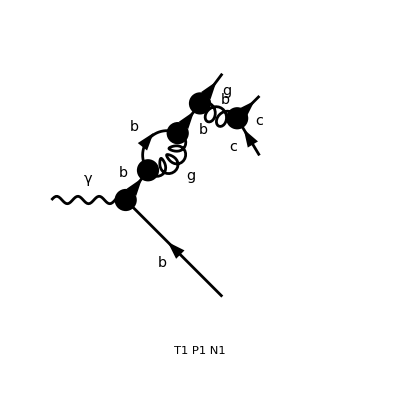

Amplitude after Fire (without PreFactor):

(4 e m^2 IntF(1/(r s+OverBar[k1]^2-2 r (OverBar[k1]·OverBar[p3])-2 (OverBar[k1]·OverBar[p4])),k1) ((4 r^2 OverBar[p3]^γ s^2)/m^4+(8 r^3 OverBar[p3]^γ s)/m^2-(4 r OverBar[p3]^γ s)/m^2+(4 r^2 OverBar[p4]^γ s)/m^2+16 r^3 OverBar[p3]^γ-40 r^2 OverBar[p3]^γ+32 r OverBar[p3]^γ-8 OverBar[p3]^γ+8 r^2 OverBar[p4]^γ-16 r OverBar[p4]^γ+8 OverBar[p4]^γ) g_s^4)/(27 r^4 s^3 (r (s/m^2-2)+r^2+1))+(4 e m^2 IntF(1/(OverBar[k1]^2 (r s+OverBar[k1]^2-2 r (OverBar[k1]·OverBar[p3])-2 (OverBar[k1]·OverBar[p4]))),k1) (-(4 r^3 OverBar[p3]^γ s^3)/m^4+(16 r^4 OverBar[p3]^γ s^2)/m^2-(16 r^3 OverBar[p3]^γ s^2)/m^2-(4 r^2 OverBar[p3]^γ s^2)/m^2+(12 r^3 OverBar[p4]^γ s^2)/m^2-(16 r^2 OverBar[p4]^γ s^2)/m^2+16 r^5 OverBar[p3]^γ s-16 r^4 OverBar[p3]^γ s-32 r^3 OverBar[p3]^γ s+48 r^2 OverBar[p3]^γ s-16 r OverBar[p3]^γ s+8 r^4 OverBar[p4]^γ s-8 r^3 OverBar[p4]^γ s-8 r^2 OverBar[p4]^γ s+8 r OverBar[p4]^γ s-16 m^2 OverBar[p3]^γ+32 m^2 r^5 OverBar[p3]^γ-144 m^2 r^4 OverBar[p3]^γ+256 m^2 r^3 OverBar[p3]^γ-224 m^2 r^2 OverBar[p3]^γ+96 m^2 r OverBar[p3]^γ+16 m^2 OverBar[p4]^γ+16 m^2 r^4 OverBar[p4]^γ-64 m^2 r^3 OverBar[p4]^γ+96 m^2 r^2 OverBar[p4]^γ-64 m^2 r OverBar[p4]^γ) g_s^4)/(27 r^4 s^3 (r (s/m^2-2)+r^2+1))+ϵ ((4 e m^2 IntF(1/(r s+OverBar[k1]^2-2 r (OverBar[k1]·OverBar[p3])-2 (OverBar[k1]·OverBar[p4])),k1) (-(8 r^2 OverBar[p3]^γ s^2)/m^4-(16 r^3 OverBar[p3]^γ s)/m^2+(12 r^2 OverBar[p3]^γ s)/m^2-(8 r^2 OverBar[p4]^γ s)/m^2+(4 r OverBar[p4]^γ s)/m^2-16 r^3 OverBar[p3]^γ+40 r^2 OverBar[p3]^γ-32 r OverBar[p3]^γ+8 OverBar[p3]^γ-8 r^2 OverBar[p4]^γ+16 r OverBar[p4]^γ-8 OverBar[p4]^γ) g_s^4)/(27 r^4 s^3 (r (s/m^2-2)+r^2+1))+(4 e m^2 IntF(1/(OverBar[k1]^2 (r s+OverBar[k1]^2-2 r (OverBar[k1]·OverBar[p3])-2 (OverBar[k1]·OverBar[p4]))),k1) ((8 r^3 OverBar[p3]^γ s^3)/m^4-(16 r^4 OverBar[p3]^γ s^2)/m^2+(20 r^3 OverBar[p3]^γ s^2)/m^2-(16 r^3 OverBar[p4]^γ s^2)/m^2+(20 r^2 OverBar[p4]^γ s^2)/m^2-16 r^5 OverBar[p3]^γ s+56 r^4 OverBar[p3]^γ s-72 r^3 OverBar[p3]^γ s+40 r^2 OverBar[p3]^γ s-8 r OverBar[p3]^γ s-8 r^4 OverBar[p4]^γ s+24 r^3 OverBar[p4]^γ s-24 r^2 OverBar[p4]^γ s+8 r OverBar[p4]^γ s) g_s^4)/(27 r^4 s^3 (r (s/m^2-2)+r^2+1)))

```mathematica
MyDiagrPlot[86]
```